```mathematica
Clear[AssociationContaining]
AssociationContaining[a_Association,keyPatterns:{(_String->(_Pattern..|_PatternTest|_Blank)..)..}]:=MatchQ[a,KeyValuePattern[keyPatterns]]
AssociationContaining[keyPatterns:{(_String->(_Pattern..|_PatternTest|_Blank)..)..}]:=Curry[AssociationContaining][keyPatterns]
```

```mathematica
Clear[asf,assf,asssf]
asf[
inps_?(
AssociationContaining[
{
("inp1"->(_Real|_Integer|_Quantity)),
("inp2"->(_Real|_Integer|_Quantity))
}])]:=(inps["inp1"]^2+Sqrt@inps["inp2"])
assf[
inp_?(
AssociationContaining[
{
"i1"->(_Real)
}])]:=inp["i1"]^2
assf[
inp_?(
AssociationContaining[
{
"i1"->(_Integer)
}])]:=inp["i1"]^(3/2)
assf[
inp_?(
AssociationContaining[
{
"i1"->(_Quantity)
}])]:=inp["i1"]^3
asssf[
inps_?(
AssociationContaining[
{
("inp1"->(_Quantity)),
("inp2"->(_Real))
}])]:=(inps["inp1"]^2+Sqrt@inps["inp2"])
TableForm@Table[
asf[<|"inp1"->Quantity[i1test,"Millielectronvolts"],"inp2"->i2test|>],
{i1test,{3,3.,42.3}},
{i2test,{3.,3.3,52.3}}
]
TableForm@Table[
assf[<|"i1"->asstest|>],
{asstest,{3,3.,54.2,Quantity[3,"Millielectronvolts"]}}
]
TableForm@Table[
asssf[<|"inp1"->Quantity[i1test,"Millielectronvolts"],"inp2"->i2test|>],
{i1test,{3,3.,42.3}},
{i2test,{3.,3.3,52.3}}
]
```

asf[<|inp1→3 meV,inp2→3.|>] | asf[<|inp1→3 meV,inp2→3.3|>] | asf[<|inp1→3 meV,inp2→52.3|>]
asf[<|inp1→3. meV,inp2→3.|>] | asf[<|inp1→3. meV,inp2→3.3|>] | asf[<|inp1→3. meV,inp2→52.3|>]
asf[<|inp1→42.3 meV,inp2→3.|>] | asf[<|inp1→42.3 meV,inp2→3.3|>] | asf[<|inp1→42.3 meV,inp2→52.3|>]

3 √3
9.
2937.64
27 meV^3

1.73205+9 meV^2 | 1.81659+9 meV^2 | 7.23187+9 meV^2
1.73205+9. meV^2 | 1.81659+9. meV^2 | 7.23187+9. meV^2
1.73205+1789.29 meV^2 | 1.81659+1789.29 meV^2 | 7.23187+1789.29 meV^2

```mathematica
Clear[makeMC]
makeMC[params_?(AssociationContaining[
{
(* Stuff to pull from other parts of the re-processing module *)
"mu"->(_Real|_Integer|_Quantity),
"eb"->(_Real|_Integer|_Quantity),
"ef"->(_Function),
"kappa"->(_Real|_Integer),
(* More exciton params, e.g. memh and egap *)
"egap"->(_Real|_Integer|_Quantity),
"memh"->(_Real|_Integer|_Quantity),
"gamex"->(_Real|_Integer|_Quantity),
(* Cavity params *)
"epscav"->(_Real|_Integer),
"Nharm"->(_Integer),
"n1"->(_Real|_Integer),
"n2"->(_Real|_Integer),
"r1"->(_Real|_Integer),
"r2"->(_Real|_Integer),
"ndbr"->(_Integer),
"nml"->(_Integer),
(* BEC params *)
"nlp"->(_Real|_Integer|_Quantity),
"tc"->(_Real|_Integer|_Quantity)
}])]:={#mu,#gamex}
```

```mathematica
Clear[makeMC]
```

## Different approach to pol/BEC stuff: make all functions take optional arguments, but just pass all parameters into a module which then assigns those values as the “defaults” - then that master function returns a dataset where the elements of the DS can be called as functions or whatever...?

```mathematica
makeMC[mu_,eb_,ef_,kappa_,egap_,memh_,gamex_,epscav_,Nharm_,n1_,n2_,r1_,r2_,ndbr_,nml_]
```

## No... try adapting how I built the DS for Xpol:

```mathematica
Map[
Association[
"mu"->#mu,
"eb"->#eb,
"ef"->#ef,
"kappa"->#kappa,
"egap"->#egap,
"memh"->#memh,
(* Calc exciton sutff *)
"mex"->(#memh/#mu),
"exres"->Function[k,UnitConvert[(#egap-#eb)+(((chb*Quantity[k,"Micrometers"^-1])^2)/(2*(#memh/#mu))),"Millielectronvolts"]]
]&
```

## Nested dependencies

Level 0 - base input parameters that specify the MC parameters, etc.
Level 1 - Only depend on level 0 params
Level 2 - Can depend on levels 0-1
etc...

```mathematica
Clear["l0*","l1*","l2*"]
```

```mathematica
l0=<|
(* Stuff to pull from other parts of the re-processing module *)
"mu"->0.15,
"eb"->Normal@onefile["evs"][[1,1]],
"ef"->Normal@onefile["efs"][[1,1]],
"kappa"->4.89,
(* More exciton params, e.g. memh and egap *)
"egap"->Quantity[1500,"Millielectronvolts"],
"memh"->4*0.15^2,
"gamex"->Quantity[10^13,"Seconds"^-1],
(* Cavity params *)
"epscav"->1,
"Nharm"->1,
"n1"->1.45,
"n2"->2.05,
"r1"->0.985,
"r2"->0.95,
"ndbr"->1,
"nml"->3,
(* BEC params *)
"nlp"->Quantity[10^15,"Meters"^-2],
"fixtc"->Quantity[300,"Kelvins"]
|>;
```

```mathematica
l1=Quiet@(<|
"xbhr"->UnitConvert[Quantity[Last[Last[Last[NMaximize[{Abs[r*((#ef[r])^2)],0≤r≤1000},r,Method->"SimulatedAnnealing"]]]],"BohrRadius"],"Nanometers"],
"psi0"->Quantity[(1/(2*Pi))*#ef[0],"BohrRadius"^-1],
"mex"->Quantity[#memh/#mu,"ElectronMass"],
"reff"->(4*#r1*#r2)/((Sqrt[#r1]+Sqrt[#r2])^2)
|>&);
```

```mathematica
l1[l0]
```

<|xbhr→0.965917 nm,psi0→0.00832243 /a_0,mex→0.6 m_e,reff→0.967263|>

#### l2 (holding on to free params like k is a PITA)

```mathematica
l2v1=Quiet@(<|
"exres"->UnitConvert[(#egap-#eb)+(((chb*Quantity[#k,"Micrometers"^-1])^2)/(2*#mex)),"Millielectronvolts"]
|>&);
```

Function::slota: Named Slot k in Association[exres→UnitConvert[(#egap-Slot[«1»])+Times[«2»]^2/Times[«2»],Millielectronvolts]]& cannot be filled from <|mu→0.15,eb→-,ef→«1»,kappa→4.89,egap→1500,memh→0.09,gamex→10000000000000,epscav→1,Nharm→1,n1→1.45,n2→2.05,r1→0.985,r2→0.95,ndbr→1,nml→3,nlp→1000000000000000,fixtc→300,xbhr→0.965917,psi0→0.00832243,mex→0.6,reff→0.967263|>.

<|exres→0.0000761996563 (2.33901×10^7+0.833333 (#k)^2) meV|>

<|exres→0.0000761996563 (2.33901×10^7+0.833333 (#k)^2) meV|>&

<|exres→0.0000761996563 (2.33901×10^7+0.833333 (#k)^2) meV|>

<|exres→0.0000761996563 (2.33901×10^7+0.833333 (#k)^2) meV|>

<|exres→0.0000761996563 (2.33901×10^7+0.833333 (#k)^2) meV|>

0.0000761996563 (2.33901×10^7+0.833333 (#k)^2) meV

0.0000761996563 (2.33901×10^7+0.833333 (#k)^2) meV

<|exres→0.0000761996563 (2.33901×10^7+0.833333 (#k)^2) meV|>

0.0000761996563 (2.33901×10^7+0.833333 (#k)^2) meV

0.0000761996563 (2.33901×10^7+0.833333 (#k)^2) meV

<|exres→1782.32 meV|>

0.0000761996563 (2.33901×10^7+0.833333 kvar^2) meV

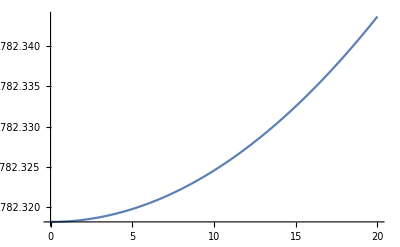

1782.34 meV

```mathematica
l2v1nok=l2v1[Union[l0,l1[l0]]];
LightRed~bg~l2v1nok
LightOrange~bg~(Evaluate[l2v1nok]&)
LightOrange~bg~(l2v1nok&)[<|"k"->0.4|>]
LightOrange~bg~((Evaluate[l2v1nok]&)[<|"k"->0.4|>])
LightOrange~bg~((Evaluate[(l2v1nok&)[<|"k"->0.4|>]]))
LightYellow~bg~l2v1nok["exres"]
LightGreen~bg~l2v1nok["exres"]&[<|"k"->20|>]
LightCyan~bg~Evaluate[l2v1nok&][<|"k"->30|>]
LightBlue~bg~Evaluate[l2v1nok["exres"]]&[<|"k"->20|>]
LightPurple~bg~Evaluate[l2v1nok["exres"]&][<|"k"->20|>]
LightMagenta~bg~(l2v1k0=l2v1[Union[l0,l1[l0],<|"k"->0|>]])
LightPink~bg~(l2v1kvar=l2v1[Union[l0,l1[l0],<|"k"->kvar|>]]["exres"])
LightBrown~bg~Plot[l2v1kvar,{kvar,0,20}]
LightBrown~bg~(l2v1kvar/.{kvar->20})
```

#### l2v2

OK so it is possible to send named arguments after the initial function call, but it’s weirdly awkward.
Couple ideas:
(1) almost definitely remove #k from the function definition since I know I’ll never be supplying that upfront.
(2) maybe make each value in the Assoc it’s own pure function?

```mathematica
l2v2=<|
"exres"->(UnitConvert[(#egap-#eb)+(((chb*Quantity[kvar,"Micrometers"^-1])^2)/(2*#mex)),"Millielectronvolts"]&)
|>;
```

```mathematica
l2v2nok=Map[#[Union[l0,l1[l0]]]&,l2v2];
LightRed~bg~l2v2nok
LightOrange~bg~(l2v2nok/.{kvar->50})
LightYellow~bg~Evaluate@(l2v2nok/.{kvar->50})
LightGreen~bg~(l2v2nok["exres"]/.{kvar->50})
LightCyan~bg~Evaluate@(l2v2nok["exres"]/.{kvar->50})
LightBlue~bg~Plot[Evaluate[l2v2nok["exres"]/.{kvar->kplt}],{kplt,0,20}]
LightPurple~bg~Plot[Evaluate[Values@l2v2nok/.{kvar->kplt}],{kplt,0,20}]
LightMagenta~bg~Plot[(Values@l2v2nok)/.{kvar->kplt},{kplt,0,20}]
LightPink~bg~Plot[l2v2nok["exres"]/.{kvar->kplt},{kplt,0,20}]
```

<|exres→0.0000761996563 (2.33901×10^7+0.833333 kvar^2) meV|>

<|exres→0.0000761996563 (2.33901×10^7+0.833333 50^2) meV|>

<|exres→0.0000761996563 (2.33901×10^7+0.833333 50^2) meV|>

1782.48 meV

1782.48 meV

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### l2v3 (Best so far)

CAVEAT: This is the best way to deal with e.g. k or de so far, but what if I wanted to vary egap? or memh and therefore mex?
Its 1:30 and I spent my entire day doing this shit. If I want to vary the input parameters I’ll wrap the “makeMC” function in a Table like a damn peasant. I’m making this way more complicated than it needs to be (but Mathematica isn’t helping).

```mathematica
l2v3=(<|
"exres"->Function[kvar,UnitConvert[(#egap-#eb)+(((chb*Quantity[kvar,"Micrometers"^-1])^2)/(2*#mex)),"Millielectronvolts"]]
|>&);
```

<|exres→Function[kvar,UnitConvert[(1500 meV--282.318 meV)+(chb (kvar /µm))^2/(2 (0.6 m_e)),Millielectronvolts]]|>

1782.36 meV

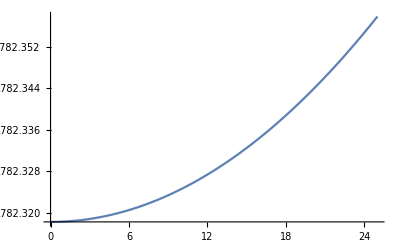

```mathematica
l2v3apply=l2v3[Union[l0,l1[l0]]]
l2v3apply["exres"][25]
Plot[l2v3apply["exres"][k],{k,0,25}]
```

Can I like MapAt this key value pair and wrap the expression with Function[ { k } , #val ] ??

OK - so doing this one level works. Now when I go deeper I need to keep the original “base” parameters and just append the newly generated values at each level
(How is this going to work when things depend on [de, k]???

```mathematica
Dataset@Union[l0,l1[l0]]
```

Dataset[<>]

## OK... doing l0,l1,l2,...,l10 is really not the way to go.

#### 1

```mathematica
Map[
<|
"exres"->Function[{k},(#eg-#eb)+(k^2)/(2*#mex)]
|>&,
<|
"allspec"-><|
"eg"->1500,
"eb"->500,
"mex"->0.6
|>,
"egfree"-><|
"eg"->Function[{eg},Quantity[eg,"Millielectronvolts"]],
"eb"->500,
"mex"->0.6
|>|>
]
```

<|allspec→<|exres→Function[{k},(1500-500)+k^2/(2 0.6)]|>,egfree→<|exres→Function[{k},(Function[{eg},eg meV]-500)+k^2/(2 0.6)]|>|>

```mathematica
tst=%
```

<|allspec→<|exres→Function[{k},(1500-500)+k^2/(2 0.6)]|>,egfree→<|exres→Function[{k},(Function[{eg},eg meV]-500)+k^2/(2 0.6)]|>|>

```mathematica
tst["allspec"]
tst["allspec"]["exres"]
tst["allspec"]["exres"][#]&/@{0,25,50}
```

<|exres→Function[{k},(1500-500)+k^2/(2 0.6)]|>

Function[{k},(1500-500)+k^2/(2 0.6)]

{1000.,1520.83,3083.33}

```mathematica
tst["egfree"]
tst["egfree"]["exres"]
tst["egfree"]["exres"][#]&/@{0,25,50}
tst["egfree"]["exres"][0]
tst["egfree"]["exres"][0][2]
tst["egfree"]["exres"][0]/.{eg->2}
```

<|exres→Function[{k},(Function[{eg},eg meV]-500)+k^2/(2 0.6)]|>

Function[{k},(Function[{eg},eg meV]-500)+k^2/(2 0.6)]

{-500.+Function[{eg},eg meV],20.8333+Function[{eg},eg meV],1583.33+Function[{eg},eg meV]}

-500.+Function[{eg},eg meV]

(-500.+Function[{eg},eg meV])[2]

Function::flpar: Parameter specification {2} in Function[{2},2] should be a symbol or a list of symbols.

-500.+Function[{2},2 meV]

```mathematica
%//InputForm
```

-500. + Function[{eg}, Quantity[eg, "Millielectronvolts"]]

```mathematica
-500. + Function[{eg}, Quantity[eg, "Millielectronvolts"]]
```

#### 2

```mathematica
tst2=Map[
<|
"exres"->Function[#exresarglist,(#eg-#eb)+(k^2)/(2*#mex)]
|>&,
<|
"allspec"-><|
"eg"->1500,
"eb"->500,
"mex"->0.6,
"exresarglist"->{k}
|>,
"egfree"-><|
"eg"->Quantity[eg,"Millielectronvolts"],
"eb"->500,
"mex"->0.6,
"exresarglist"->{k,eg}
|>|>
]
```

<|allspec→<|exres→Function[{k},(1500-500)+k^2/(2 0.6)]|>,egfree→<|exres→Function[{k,eg},(eg meV-500)+k^2/(2 0.6)]|>|>

```mathematica
tst2["allspec","exres"][50]
tst2["egfree","exres"][50,1500]
```

3083.33

1583.33+1500 meV

#### 3

Oh shit! that worked!
OK - now the move is to take the mapping function, <|”exres”->[...]|> in this case, and make them explicit functions with explicitly specified lists of arguments which are located at the second level of the mapped-to association, e.g. <|”allspec”-><|...|>,”egfree”-><|...|>|>
What about more nesting in the mapped-to assoc, and taking advantage of levelspec in Map[] so that it applies repeatedly down the levels???

```mathematica
tst3=Map[
<|
"exres"->Function[#exresargs,(#eg-#eb)+((chb*Quantity[k,"Micrometers"^(-1)])^2)/(2*#mex)],
"ecav"->Function[#ecavargs,((#eg-#eb)*(1+de))+(((chb*ccc*Quantity[k,"Micrometers"^(-1)])^2)/(2*#epscav*((#eg-#eb)*(1+de))))],
"mcav"->Function[#mcavargs,#epscav*((#eg-#eb)*(1+de))/(ccc^2)]
|>&,
<|
"open1dbrdefault"-><|
"eg"->Quantity[1500,"Millielectronvolts"],
"eb"->Quantity[560,"Millielectronvolts"],
"epscav"->1,
"mex"->Quantity[0.6,"ElectronMass"],
"exresargs"->{k},
"ecavargs"->{k,de},
"mcavargs"->{k,de}
|>,
"open1dbrfreemex"-><|
"eg"->Quantity[1500,"Millielectronvolts"],
"eb"->Quantity[560,"Millielectronvolts"],
"epscav"->1,
"mex"->Quantity[mex,"ElectronMass"],
"exresargs"->{mex,k},
"ecavargs"->{k,de},
"mcavargs"->{k,de}
|>
|>]
```

<|open1dbrdefault→<|exres→Function[{k},(1500 meV-560 meV)+(chb (k /µm))^2/(2 (0.6 m_e))],ecav→Function[{k,de},(1500 meV-560 meV) (1+de)+(chb ccc (k /µm))^2/(2 ((1500 meV-560 meV) (1+de)))],mcav→Function[{k,de},((1500 meV-560 meV) (1+de))/ccc^2]|>,open1dbrfreemex→<|exres→Function[{mex,k},(1500 meV-560 meV)+(chb (k /µm))^2/(2 (mex m_e))],ecav→Function[{k,de},(1500 meV-560 meV) (1+de)+(chb ccc (k /µm))^2/(2 ((1500 meV-560 meV) (1+de)))],mcav→Function[{k,de},((1500 meV-560 meV) (1+de))/ccc^2]|>|>

```mathematica
tst3["open1dbrdefault","exres"][50]
tst3["open1dbrdefault","ecav"][50,0.01]
tst3["open1dbrdefault","mcav"][50,0.01]
tst3["open1dbrfreemex","exres"][0.5,50]
tst3["open1dbrfreemex","ecav"][50,0.01]
tst3["open1dbrfreemex","mcav"][50,0.01]
```

1.23381×10^7 ℏ^2/(m_e µm^2)

52215.9 meV

949.4 meV/c^2

1.23385×10^7 ℏ^2/(m_e µm^2)

52215.9 meV

949.4 meV/c^2

#### 4

```mathematica
tst4=Map[
<|
"exres"->Function[#exresargs,(#eg-#eb)+((chb*Quantity[k,"Micrometers"^(-1)])^2)/(2*#mex)],
"ecav"->Function[#ecavargs,((#eg-#eb)*(1+de))+(((chb*ccc*Quantity[k,"Micrometers"^(-1)])^2)/(2*#epscav*((#eg-#eb)*(1+de))))],
"mcav"->Function[#mcavargs,#epscav*((#eg-#eb)*(1+de))/(ccc^2)]
|>&,
<|
"open1dbrdefault"-><|
"eg"->Quantity[1500,"Millielectronvolts"],
"eb"->Quantity[560,"Millielectronvolts"],
"epscav"->1,
"mex"->Quantity[0.6,"ElectronMass"],
"exresargs"->{k},
"ecavargs"->{k,de},
"mcavargs"->{k,de}
|>,
"open1dbrfreemex"-><|
"eg"->Quantity[1500,"Millielectronvolts"],
"eb"->Quantity[560,"Millielectronvolts"],
"epscav"->1,
"mex"->Quantity[mex,"ElectronMass"],
"exresargs"->{mex,k},
"ecavargs"->{k,de},
"mcavargs"->{k,de}
|>
|>]
```